# Effective Higgs Potential

We derive the 1-loop renormalization constants of the SM. Compute the running of the masses, couplings and fields. Calculate the 1-loop effective higgs potential, and use the renormalization group equation to resum the logarithms.

## Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
description="Renormalization of the SM";
If[$FrontEnd===Null,$FeynCalcStartupMessages=False;
Print[description];];
If[$Notebooks===False,$FeynCalcStartupMessages=False];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;

FCCheckVersion[9,3,1];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
$KeepLogDivergentScalelessIntegrals=True;
```

```mathematica
FAPatch[PatchModelsOnly -> True];
```

Successfully patched FeynArts.

## Renormalization of the SM

## Higgs Self-Energy

```mathematica
params={InsertionLevel->{Particles},Model->FileNameJoin[{"SMQCD"}]};
top[i_,j_]:=CreateTopologies[1,i->j];
topCT[i_,j_]:=CreateCTTopologies[1,i->j];
topVertex[i_,j_]:=CreateTopologies[1,i->j,ExcludeTopologies->{WFCorrectionCTs}];
topVertexCT[i_,j_]:=CreateCTTopologies[1,i->j,ExcludeTopologies->{WFCorrectionCTs}];

{diagHiggsSE,diagHiggsSECT}=InsertFields[#,{S[1]}->{S[1]},Sequence@@params, ExcludeParticles->{F[3|4,{1|2}],F[4,{3}], F[2]}]&/@{top[1,1],topCT[1,1]};
{diagVertex,diagVertexCT}=InsertFields[#,{S[1],S[1]}->{S[1],S[1]},Sequence@@params, ExcludeParticles->{F[3|4,{1|2}],F[4,{3}]}]&/@{topVertex[2,2],topVertexCT[2,2]};

diag1[0]=diagHiggsSE[[0]][Sequence@@diagHiggsSE,Sequence@@diagHiggsSECT];
diag2[0]=diagVertex[[0]][Sequence@@diagVertex,Sequence@@diagVertexCT];
```

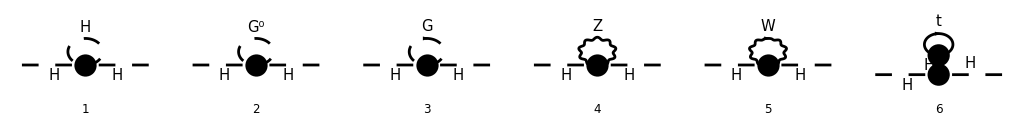

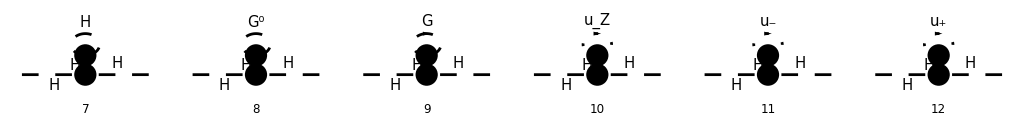

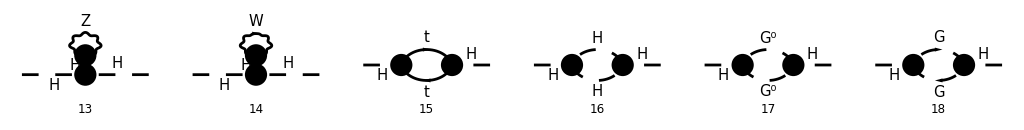

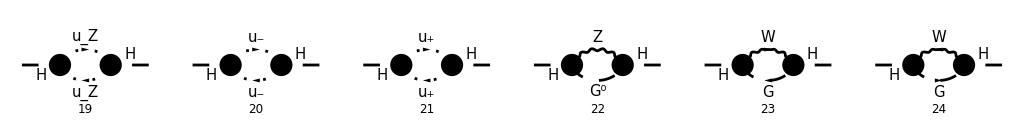

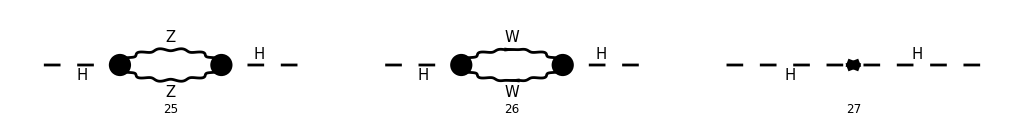

```mathematica
Paint[diag1[0],ColumnsXRows->{6,1},SheetHeader->None,Numbering->Simple,ImageSize->{1024,130}];
```

```mathematica
amp1[0]=FCFAConvert[CreateFeynAmp[diag1[0],Truncated->True,GaugeRules->{},PreFactor->1],IncomingMomenta->{p},OutgoingMomenta->{p},LorentzIndexNames->{mu, nu, rho, sigma},LoopMomenta->{l},UndoChiralSplittings->True,ChangeDimension->D,List->False,SMP->True,FinalSubstitutions->{dZH1-> dZH1/Epsilon, dMHsq1-> dMHsq1 SMP["m_H"]^2/Epsilon,GaugeXi[S[1]]->GaugeXi, GaugeXi[W]-> GaugeXi, GaugeXi[g]-> GaugeXi, GaugeXi[Z]-> GaugeXi,FeynAmpDenominator[PropagatorDenominator[0,SMP["m_H"]]]-> -1/SMP["m_H"]^2}]
```

(9 e^2 m_H^4)/(8 (l^2-m_H^2).((l-p)^2-m_H^2) m_W^2 (sin(θ_W))^2)+(e^2 m_H^4)/(4 (l^2-ξ m_W^2).((l-p)^2-ξ m_W^2) m_W^2 (sin(θ_W))^2)+(e^2 m_H^4)/(8 (l^2-ξ m_Z^2).((l-p)^2-ξ m_Z^2) m_W^2 (sin(θ_W))^2)+(3 g^munu e^2 (((1-ξ) l^mu l^nu)/((l^2-m_W^2).(l^2-ξ m_W^2) m_H^2)-g^munu/((l^2-m_W^2) m_H^2)) m_H^2)/(2 (sin(θ_W))^2)+(3 g^munu e^2 (((1-ξ) l^mu l^nu)/((l^2-m_Z^2).(l^2-ξ m_Z^2) m_H^2)-g^munu/((l^2-m_Z^2) m_H^2)) m_H^2)/(4 (cos(θ_W))^2 (sin(θ_W))^2)-(3 e^2 m_H^2)/(4 (l^2-m_H^2) m_W^2 (sin(θ_W))^2)-(e^2 m_H^2)/(2 (l^2-ξ m_W^2) m_W^2 (sin(θ_W))^2)-(e^2 m_H^2)/(4 (l^2-ξ m_Z^2) m_W^2 (sin(θ_W))^2)+(ⅈ dZH1 p^2)/ε-ⅈ ((dMHsq1 m_H^2)/ε+(dZH1 m_H^2)/ε)+(tr((m_t-γ·l).(-(ⅈ e m_t)/(2 m_W (sin(θ_W)))).(γ·(p-l)+m_t).(-(ⅈ e m_t)/(2 m_W (sin(θ_W))))) SumOver(Col3,3))/((l^2-m_t^2).((l-p)^2-m_t^2))+(3 ⅈ tr((m_t-γ·l).(-(ⅈ e m_t)/(2 m_W (sin(θ_W))))) e SumOver(Col3,3))/(2 (l^2-m_t^2) m_W (sin(θ_W)))+(3 ξ e^2)/(2 (l^2-ξ m_W^2) (sin(θ_W))^2)+(g^munu (g^munu/(l^2-m_W^2)-((1-ξ) l^mu l^nu)/((l^2-m_W^2).(l^2-ξ m_W^2))) e^2)/(2 (sin(θ_W))^2)+((l+p)^mu (-l-p)^nu (g^munu/((l^2-ξ m_W^2).((l-p)^2-m_W^2))+((1-ξ) (l-p)^mu (p-l)^nu)/((l^2-ξ m_W^2).((l-p)^2-m_W^2).((l-p)^2-ξ m_W^2))) e^2)/(2 (sin(θ_W))^2)+(g^munu (g^munu/(l^2-m_Z^2)-((1-ξ) l^mu l^nu)/((l^2-m_Z^2).(l^2-ξ m_Z^2))) e^2)/(4 (cos(θ_W))^2 (sin(θ_W))^2)+((l+p)^mu (-l-p)^nu (g^munu/((l^2-ξ m_Z^2).((l-p)^2-m_Z^2))+((1-ξ) (l-p)^mu (p-l)^nu)/((l^2-ξ m_Z^2).((l-p)^2-m_Z^2).((l-p)^2-ξ m_Z^2))) e^2)/(4 (cos(θ_W))^2 (sin(θ_W))^2)-(ξ^2 e^2 m_W^2)/(2 (l^2-ξ m_W^2).((l-p)^2-ξ m_W^2) (sin(θ_W))^2)+(g^murho g^nusigma (-((1-ξ)^2 l^mu l^nu (l-p)^rho (p-l)^sigma)/((l^2-m_W^2).(l^2-ξ m_W^2).((l-p)^2-m_W^2).((l-p)^2-ξ m_W^2))-((1-ξ) l^mu l^nu g^rhosigma)/((l^2-m_W^2).(l^2-ξ m_W^2).((l-p)^2-m_W^2))+((1-ξ) g^munu (l-p)^rho (p-l)^sigma)/((l^2-m_W^2).((l-p)^2-m_W^2).((l-p)^2-ξ m_W^2))+(g^munu g^rhosigma)/((l^2-m_W^2).((l-p)^2-m_W^2))) e^2 m_W^2)/(sin(θ_W))^2+(g^murho g^nusigma (-((1-ξ)^2 l^mu l^nu (l-p)^rho (p-l)^sigma)/((l^2-m_Z^2).(l^2-ξ m_Z^2).((l-p)^2-m_Z^2).((l-p)^2-ξ m_Z^2))-((1-ξ) l^mu l^nu g^rhosigma)/((l^2-m_Z^2).(l^2-ξ m_Z^2).((l-p)^2-m_Z^2))+((1-ξ) g^munu (l-p)^rho (p-l)^sigma)/((l^2-m_Z^2).((l-p)^2-m_Z^2).((l-p)^2-ξ m_Z^2))+(g^munu g^rhosigma)/((l^2-m_Z^2).((l-p)^2-m_Z^2))) e^2 m_W^2)/(2 (cos(θ_W))^4 (sin(θ_W))^2)-(ξ^2 e^2 m_Z^2)/(4 (l^2-ξ m_Z^2).((l-p)^2-ξ m_Z^2) (cos(θ_W))^2 (sin(θ_W))^2)+(3 ξ e^2 m_Z)/(4 (l^2-ξ m_Z^2) (cos(θ_W)) m_W (sin(θ_W))^2)

```mathematica
amp1[1]=amp1[0]//SUNSimplify//DiracSimplify//TID[#,l,UsePaVeBasis->True,ToPaVe->True]&
```

(9 ⅈ π^2 B_0(p^2,m_H^2,m_H^2) e^2 m_H^4)/(8 m_W^2 (sin(θ_W))^2)-(3 ⅈ π^2 A_0(m_H^2) e^2 m_H^2)/(4 m_W^2 (sin(θ_W))^2)+(ⅈ (-dMHsq1 m_H^2-dZH1 m_H^2+dZH1 p^2))/ε+(2 ⅈ π^2 A_0(m_t^2) e^2 m_t^2 SumOver(Col3,3))/(m_W^2 (sin(θ_W))^2)+(ⅈ π^2 B_0(p^2,m_t^2,m_t^2) e^2 m_t^2 (p^2-4 m_t^2) SumOver(Col3,3))/(2 m_W^2 (sin(θ_W))^2)-(ⅈ π^2 A_0(m_W^2) e^2 (2 D m_W^2-2 m_W^2+p^2))/(2 m_W^2 (sin(θ_W))^2)+(ⅈ π^2 B_0(p^2,m_W^2,m_W^2) e^2 (4 D m_W^4-4 m_W^4-4 p^2 m_W^2+p^4))/(4 m_W^2 (sin(θ_W))^2)-(ⅈ π^2 A_0(m_Z^2) e^2 (2 D m_Z^2 (cos(θ_W))^2-ξ m_Z^2 (cos(θ_W))^2-m_Z^2 (cos(θ_W))^2+p^2 (cos(θ_W))^2+ξ m_W^2-m_W^2))/(4 (cos(θ_W))^4 m_Z^2 (sin(θ_W))^2)+(ⅈ π^2 A_0(ξ m_Z^2) e^2 (-m_H^2 m_Z^2 (cos(θ_W))^4+3 ξ m_W m_Z^3 (cos(θ_W))^3+p^2 m_W^2 (cos(θ_W))^2-4 ξ m_W^2 m_Z^2 (cos(θ_W))^2+m_W^2 m_Z^2 (cos(θ_W))^2+ξ m_W^4-m_W^4))/(4 (cos(θ_W))^4 m_W^2 m_Z^2 (sin(θ_W))^2)+(ⅈ π^2 B_0(p^2,m_Z^2,m_Z^2) e^2 m_W^2 (4 D m_Z^4-4 m_Z^4-4 p^2 m_Z^2+p^4))/(8 (cos(θ_W))^4 m_Z^4 (sin(θ_W))^2)-(ⅈ π^2 B_0(p^2,m_Z^2,ξ m_Z^2) e^2 (m_W^2-(cos(θ_W))^2 m_Z^2) (ξ^2 m_Z^4-2 ξ m_Z^4+m_Z^4-2 ξ p^2 m_Z^2-2 p^2 m_Z^2+p^4))/(4 (cos(θ_W))^4 m_Z^4 (sin(θ_W))^2)+(ⅈ π^2 B_0(p^2,ξ m_Z^2,ξ m_Z^2) e^2 (-4 ξ^2 (cos(θ_W))^2 m_W^2 m_Z^6+(cos(θ_W))^4 m_H^4 m_Z^4+4 ξ^2 m_W^4 m_Z^4+4 ξ p^2 (cos(θ_W))^2 m_W^2 m_Z^4-4 ξ p^2 m_W^4 m_Z^2-2 p^4 (cos(θ_W))^2 m_W^2 m_Z^2+p^4 m_W^4))/(8 (cos(θ_W))^4 m_W^2 m_Z^4 (sin(θ_W))^2)+(ⅈ π^2 A_0(ξ m_W^2) e^2 (p^2-m_H^2))/(2 m_W^2 (sin(θ_W))^2)-(ⅈ π^2 B_0(p^2,ξ m_W^2,ξ m_W^2) e^2 (p^4-m_H^4))/(4 m_W^2 (sin(θ_W))^2)

```mathematica
amp1[2] = amp1[1]//PaVeUVPart[#,Prefactor->1/(2 Pi)^D]&
```

-1/((D-4) ε m_W^2 (cos(θ_W))^4 (sin(θ_W))^2)ⅈ 2^(-D-1) π^-D (2 π^2 e^2 ε p^2 m_t^2 SumOver(Col3,3) (cos(θ_W))^4-2^(D+3) π^D dMHsq1 m_H^2 m_W^2 (cos(θ_W))^4 (sin(θ_W))^2+2^(D+1) D π^D dMHsq1 m_H^2 m_W^2 (cos(θ_W))^4 (sin(θ_W))^2-2^(D+3) π^D dZH1 m_H^2 m_W^2 (cos(θ_W))^4 (sin(θ_W))^2+2^(D+1) D π^D dZH1 m_H^2 m_W^2 (cos(θ_W))^4 (sin(θ_W))^2+2^(D+3) π^D dZH1 p^2 m_W^2 (cos(θ_W))^4 (sin(θ_W))^2-2^(D+1) D π^D dZH1 p^2 m_W^2 (cos(θ_W))^4 (sin(θ_W))^2-2 π^2 e^2 ε ξ m_H^2 m_W^2 (cos(θ_W))^4+3 π^2 e^2 ε m_H^4 (cos(θ_W))^4-π^2 e^2 ε ξ m_H^2 m_Z^2 (cos(θ_W))^4+2 π^2 e^2 ε ξ p^2 m_W^2 (cos(θ_W))^4+π^2 e^2 ε ξ p^2 m_W^2 (cos(θ_W))^2-6 π^2 e^2 ε p^2 m_W^2 (cos(θ_W))^4-3 π^2 e^2 ε p^2 m_W^2 (cos(θ_W))^2+3 π^2 e^2 ε ξ^2 m_W m_Z^3 (cos(θ_W))^3-5 π^2 e^2 ε ξ^2 m_W^2 m_Z^2 (cos(θ_W))^2-6 π^2 e^2 ε m_W^2 m_Z^2 (cos(θ_W))^2+2 π^2 e^2 ε ξ^2 m_W^4+6 π^2 e^2 ε m_W^4)

```mathematica
amp1[3] = FCReplaceD[amp1[2],D->4-2 Epsilon]//Series[#,{Epsilon,0,-1}]&//Normal//Simplify
```

(ⅈ ((cos(θ_W))^4 (e^2 (2 p^2 (m_t^2 SumOver(Col3,3)+(ξ-3) m_W^2)-ξ m_H^2 (2 m_W^2+m_Z^2)+3 m_H^4)+64 π^2 m_W^2 (sin(θ_W))^2 (dZH1 p^2-(dMHsq1+dZH1) m_H^2))+e^2 m_W^2 (cos(θ_W))^2 ((ξ-3) p^2-(5 ξ^2+6) m_Z^2)+3 e^2 ξ^2 m_W m_Z^3 (cos(θ_W))^3+2 e^2 (ξ^2+3) m_W^4))/(64 π^2 ε m_W^2 (cos(θ_W))^4 (sin(θ_W))^2)

```mathematica
mTerms=SelectFree2[amp1[3], p]//Simplify
```

-(ⅈ (m_H^2 (cos(θ_W))^4 (64 π^2 (dMHsq1+dZH1) m_W^2 (sin(θ_W))^2+e^2 (-3 m_H^2+2 ξ m_W^2+ξ m_Z^2))-3 e^2 ξ^2 m_W m_Z^3 (cos(θ_W))^3+e^2 (5 ξ^2+6) m_W^2 m_Z^2 (cos(θ_W))^2-2 e^2 (ξ^2+3) m_W^4))/(64 π^2 ε m_W^2 (cos(θ_W))^4 (sin(θ_W))^2)

```mathematica
pTerms=SelectNotFree2[amp1[3], p]
```

(ⅈ e^2 p^2 (m_t^2 SumOver(Col3,3)+(ξ-3) m_W^2))/(32 π^2 ε m_W^2 (sin(θ_W))^2)+(ⅈ e^2 (ξ-3) p^2)/(64 π^2 ε (cos(θ_W))^2 (sin(θ_W))^2)+(ⅈ dZH1 p^2)/ε

```mathematica
amp1[3] - mTerms - pTerms //Simplify
```

0

```mathematica
dZH1replace={dZH1-> Collect[Normal[Simplify[dZH1/.Solve[pTerms==0, dZH1][[1]]/.{SMP["Delta"]->1/Epsilon}/.{SumOver[__, 3]-> Nc,SMP["m_t"]-> Y*v/√2, SMP["m_W"]-> v/2 g2, SMP["m_Z"]-> v/2 √(g2^2 + gY^2), SMP["e"]-> g2*SMP["sin_W"], SMP["cos_W"]-> g2/(√(g2^2 + gY^2)), SMP["m_H"]-> √(2 λ) v}]],{gY, g2, Y},Simplify]}
```

{dZH1→-(3 g2^2 (ξ-3))/(64 π^2)-(gY^2 (ξ-3))/(64 π^2)-(Nc Y^2)/(16 π^2)}

```mathematica
dZHMsq1replace={dMHsq1-> Collect[Normal[Simplify[dMHsq1/.Solve[mTerms==0, dMHsq1][[1]]/.dZH1replace/.{SumOver[__, 3]-> Nc,SMP["m_t"]-> Y*v/√2, SMP["m_W"]-> v/2 g2, SMP["m_Z"]-> v/2 √(g2^2 + gY^2), SMP["e"]-> g2*SMP["sin_W"], SMP["cos_W"]-> g2/(√(g2^2 + gY^2)), SMP["m_H"]-> √(2 λ) v}]],{gY, g2, Y},Simplify]}
```

{dMHsq1→-(9 g2^2)/(64 π^2)-(3 gY^2)/(64 π^2)+(3 λ)/(8 π^2)+(Nc Y^2)/(16 π^2)}

```mathematica
V0 = 1/2 mu2 ϕ^2 + 1/4 λ ϕ^4;
V⃛Vector = 3 (2 g2^4 + (g2^2 + gY^2)^2)/(1024 Pi^2) ϕ^4 Log[ϕ^2/μ^2];
V⃛Fermion =- 3 Y^4/(64 Pi^2) ϕ^4 Log[ϕ^2/μ^2];
V⃛Scalar =  ((mu2 + 3 λ ϕ^2)^2)/(64 Pi^2)  Log[(ϕ^2 + 3 λ ϕ^2)/μ^2] + (3(mu2 +  λ ϕ^2)^2)/(64 Pi^2)  Log[(ϕ^2 +  λ ϕ^2)/μ^2];
```

```mathematica
V1 = V⃛Vector + V⃛Fermion + V⃛Scalar;
```

```mathematica
γH = (-9 g2^2 - 3 gY^2 + 12 Y^2) 1/(64 Pi^2);
```

```mathematica
lhs=βλ D[V0, λ] + βmu2 mu2 D[V0, mu2] - γH ϕ D[V0, ϕ]//Simplify
```

1/64 ϕ (16 βλ ϕ^3+(3 ϕ (3 g2^2+gY^2-4 Y^2) (λ ϕ^2+mu2))/π^2+32 βmu2 mu2 ϕ)

```mathematica
rhs=-μ D[V1, μ]//Simplify
```

(3 ϕ^4 (2 g2^2 gY^2+3 g2^4+gY^4+64 λ^2-16 Y^4)+64 mu2^2+192 λ mu2 ϕ^2)/(512 π^2)

```mathematica
βλsol=Solve[Coefficient[lhs, ϕ, 4]== Coefficient[rhs, ϕ,4], βλ][[1]]//Simplify
```

{βλ→(3 (2 g2^2 (gY^2-12 λ)+3 g2^4-8 gY^2 λ+gY^4+64 λ^2+32 λ Y^2-16 Y^4))/(128 π^2)}

```mathematica
βmu2sol=Solve[Coefficient[lhs, ϕ, 2]== Coefficient[rhs, ϕ,2], βmu2][[1]]
```

{βmu2→-(3 (3 g2^2+gY^2-8 λ-4 Y^2))/(32 π^2)}

```mathematica
βmu2 - (2 γH + 3 λ/(4 Pi^2))/.βmu2sol//Simplify
```

0

```mathematica
βλ - ( 4λ γH + (24 λ^2 + 3/4 g2^4 + 3/8 (gY^2 + g2^2)^2 -  6 Y^4)1/(16 Pi^2))/.βλsol//Simplify
```

0

## Vector Boson Renormalization

```mathematica
params={InsertionLevel->{Particles},Model->FileNameJoin[{"SMQCD"}]};
top[i_,j_]:=CreateTopologies[1,i->j];
topCT[i_,j_]:=CreateCTTopologies[1,i->j];
topVertex[i_,j_]:=CreateTopologies[1,i->j,ExcludeTopologies->{Tadpoles,WFCorrections,WFCorrectionCTs,SelfEnergies}];
topVertexCT[i_,j_]:=CreateCTTopologies[1,i->j,ExcludeTopologies->{Tadpoles,WFCorrections,WFCorrectionCTs,SelfEnergies}]
```

### Z Self-Energy

```mathematica
{diagZSE,diagZSECT}=InsertFields[#,{V[2]}->{V[2]},Sequence@@params, ExcludeParticles->{F[3|4,{1|2}],F[4,{3}], F[2]}]&/@{top[1,1],topCT[1,1]};
```

```mathematica
diag1[0]=diagZSE[[0]][Sequence@@diagZSE,Sequence@@diagZSECT];
```

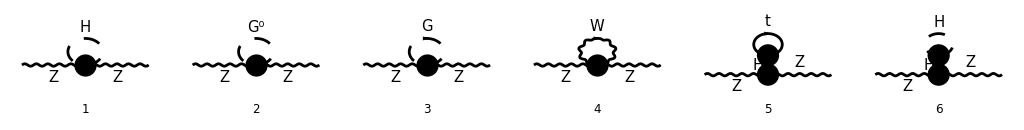

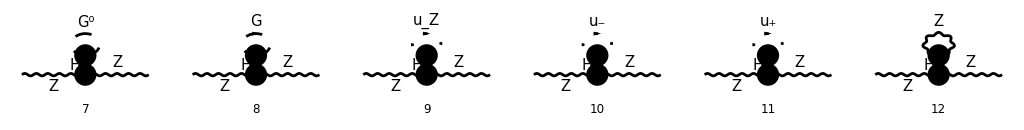

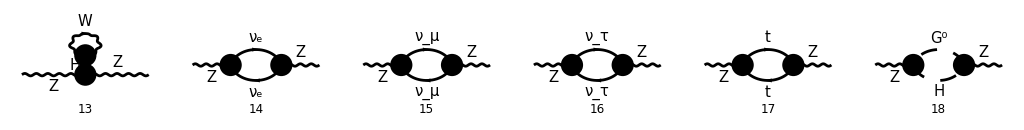

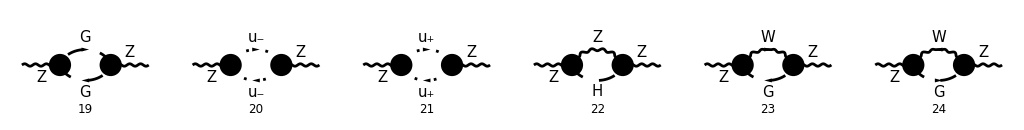

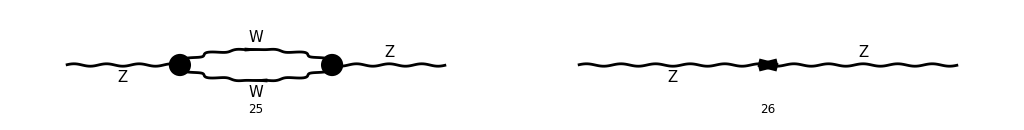

```mathematica
Paint[diag1[0],ColumnsXRows->{6,1},SheetHeader->None,Numbering->Simple,ImageSize->{1024,130}];
```

```mathematica
amp1[0]=FCFAConvert[CreateFeynAmp[diag1[0],Truncated->True,GaugeRules->{},PreFactor->1],IncomingMomenta->{p},OutgoingMomenta->{p},LorentzIndexNames->{mu, nu, rho, sigma},LoopMomenta->{l},UndoChiralSplittings->True,ChangeDimension->D,List->False,SMP->True,FinalSubstitutions->{dZZZ1-> dZZZ1/Epsilon, dMZsq1-> dMZsq1 SMP["m_Z"]^2/Epsilon,GaugeXi[S[1]]->GaugeXi, GaugeXi[W]-> GaugeXi, GaugeXi[g]-> GaugeXi, GaugeXi[Z]-> GaugeXi,FeynAmpDenominator[PropagatorDenominator[0,SMP["m_H"]]]-> -1/SMP["m_H"]^2}];
```

```mathematica
amp1[1]=amp1[0]//SUNSimplify//DiracSimplify//TID[#,l,UsePaVeBasis->True,ToPaVe->True]&;
```

```mathematica
amp1[2] = amp1[1]//PaVeUVPart[#,Prefactor->1/(2 Pi)^D]&;
```

```mathematica
amp1[3] = FCReplaceD[amp1[2],D->4-2 Epsilon]//Series[#,{Epsilon,0,-1}]&//Normal//DiracSimplify//Simplify
```

1/(1728 π^2 ε m_H^2 (cos(θ_W))^4 (sin(θ_W))^2)ⅈ (g^munu (27 (e^2 (cos(θ_W))^2 (m_H^2 (2 m_t^2 SumOver(Col3,3)-2 m_W^2 ((ξ+3) (sin(θ_W))^4-ξ)+ξ m_Z^2)-8 m_t^4 SumOver(Col3,3)+3 m_H^4+12 m_W^4)+64 π^2 (dMZsq1+dZZZ1) m_H^2 m_Z^2 (cos(θ_W))^4 (sin(θ_W))^2+2 e^2 (ξ+3) m_H^2 m_W^2 (cos(θ_W))^6-2 e^2 ξ^2 m_W m_Z^3 (cos(θ_W))+e^2 m_W^2 (2 (ξ^2+3) m_Z^2-(ξ+3) m_H^2))-p^2 m_H^2 (cos(θ_W))^2 (e^2 (-48 SumOver(Col3,3) (sin(θ_W))^2+(64 SumOver(Col3,3)+9) (sin(θ_W))^4+9 (2 SumOver(Col3,3)+7)-18 (cos(θ_W))^2 (sin(θ_W))^2+27 (4 ξ-17) (cos(θ_W))^4)+1728 π^2 dZZZ1 (cos(θ_W))^2 (sin(θ_W))^2))+m_H^2 p^mu p^nu (cos(θ_W))^2 (e^2 (-48 SumOver(Col3,3) (sin(θ_W))^2+(64 SumOver(Col3,3)+9) (sin(θ_W))^4+9 (2 SumOver(Col3,3)+7)-18 (cos(θ_W))^2 (sin(θ_W))^2+27 (4 ξ-17) (cos(θ_W))^4)+1728 π^2 dZZZ1 (cos(θ_W))^2 (sin(θ_W))^2))

```mathematica
amp1[3]=amp1[3]/.{SumOver[__, 3]-> Nc}
```

1/(1728 π^2 ε m_H^2 (cos(θ_W))^4 (sin(θ_W))^2)ⅈ (g^munu (27 (64 π^2 (dMZsq1+dZZZ1) m_H^2 m_Z^2 (cos(θ_W))^4 (sin(θ_W))^2+e^2 (cos(θ_W))^2 (m_H^2 (2 Nc m_t^2-2 m_W^2 ((ξ+3) (sin(θ_W))^4-ξ)+ξ m_Z^2)+3 m_H^4-8 Nc m_t^4+12 m_W^4)+2 e^2 (ξ+3) m_H^2 m_W^2 (cos(θ_W))^6-2 e^2 ξ^2 m_W m_Z^3 (cos(θ_W))+e^2 m_W^2 (2 (ξ^2+3) m_Z^2-(ξ+3) m_H^2))-p^2 m_H^2 (cos(θ_W))^2 (1728 π^2 dZZZ1 (cos(θ_W))^2 (sin(θ_W))^2+e^2 (-18 (cos(θ_W))^2 (sin(θ_W))^2+27 (4 ξ-17) (cos(θ_W))^4+(64 Nc+9) (sin(θ_W))^4-48 Nc (sin(θ_W))^2+9 (2 Nc+7))))+m_H^2 p^mu p^nu (cos(θ_W))^2 (1728 π^2 dZZZ1 (cos(θ_W))^2 (sin(θ_W))^2+e^2 (-18 (cos(θ_W))^2 (sin(θ_W))^2+27 (4 ξ-17) (cos(θ_W))^4+(64 Nc+9) (sin(θ_W))^4-48 Nc (sin(θ_W))^2+9 (2 Nc+7))))

```mathematica
pTerms=SelectNotFree2[amp1[3], p]
```

(ⅈ p^mu p^nu (1728 π^2 dZZZ1 (cos(θ_W))^2 (sin(θ_W))^2+e^2 (-18 (cos(θ_W))^2 (sin(θ_W))^2+27 (4 ξ-17) (cos(θ_W))^4+(64 Nc+9) (sin(θ_W))^4-48 Nc (sin(θ_W))^2+9 (2 Nc+7))))/(1728 π^2 ε (cos(θ_W))^2 (sin(θ_W))^2)-(ⅈ p^2 g^munu (1728 π^2 dZZZ1 (cos(θ_W))^2 (sin(θ_W))^2+e^2 (-18 (cos(θ_W))^2 (sin(θ_W))^2+27 (4 ξ-17) (cos(θ_W))^4+(64 Nc+9) (sin(θ_W))^4-48 Nc (sin(θ_W))^2+9 (2 Nc+7))))/(1728 π^2 ε (cos(θ_W))^2 (sin(θ_W))^2)

```mathematica
mTerms =SelectFree2[amp1[3], p]
```

1/(64 π^2 ε m_H^2 (cos(θ_W))^4 (sin(θ_W))^2)ⅈ g^munu (64 π^2 (dMZsq1+dZZZ1) m_H^2 m_Z^2 (cos(θ_W))^4 (sin(θ_W))^2+e^2 (cos(θ_W))^2 (m_H^2 (2 Nc m_t^2-2 m_W^2 ((ξ+3) (sin(θ_W))^4-ξ)+ξ m_Z^2)+3 m_H^4-8 Nc m_t^4+12 m_W^4)+2 e^2 (ξ+3) m_H^2 m_W^2 (cos(θ_W))^6-2 e^2 ξ^2 m_W m_Z^3 (cos(θ_W))+e^2 m_W^2 (2 (ξ^2+3) m_Z^2-(ξ+3) m_H^2))

```mathematica
dZZZ1replace={dZZZ1-> Collect[Normal[Simplify[dZZZ1/.Solve[pTerms==0, dZZZ1][[1]]/.{SMP["Delta"]->1/Epsilon}/.{SumOver[__, 3]-> Nc,SMP["m_t"]-> Y*v/√2, SMP["m_W"]-> v/2 g2, SMP["m_Z"]-> v/2 √(g2^2 + gY^2), SMP["e"]-> g2*SMP["sin_W"], SMP["cos_W"]-> g2/(√(g2^2 + gY^2)), SMP["m_H"]-> √(2 λ) v}]],{gY, g2, Y},Simplify]}
```

{dZZZ1→-(9 (2 g2^2 gY^2 (2 Nc+7)+2 g2^4 (6 ξ+Nc-22)+gY^4 (2 Nc+7))+(64 Nc+9) (g2^2+gY^2)^2 (sin(θ_W))^4-6 (g2^2+gY^2) (g2^2 (8 Nc+3)+8 gY^2 Nc) (sin(θ_W))^2)/(1728 π^2 (g2^2+gY^2))}

```mathematica
dMZsqreplace={dMZsq1-> Collect[Normal[Simplify[dMZsq1/.Solve[mTerms==0, dMZsq1][[1]]/.dZZZ1replace/.{SMP["Delta"]->1/Epsilon}//.{SumOver[__, 3]-> Nc,SMP["m_t"]-> Y*v/√2, SMP["m_W"]-> v/2 g2, SMP["m_Z"]-> v/2 √(g2^2 + gY^2), SMP["e"]-> g2*SMP["sin_W"], SMP["cos_W"]-> g2/(√(g2^2 + gY^2)),SMP["sin_W"]-> gY/(√(g2^2 + gY^2)), SMP["m_H"]-> √(2 λ) v}]],{gY, g2, Y, λ},Simplify]}
```

{dMZsq1→-(9 g2^4 (45 gY^2+4 λ (53-2 Nc))+3 g2^2 (16 gY^2 λ (Nc-36)+81 gY^4+144 (6 λ^2+λ Nc Y^2-Nc Y^4))+243 g2^6-68 gY^4 λ (2 Nc+9)+432 gY^2 (6 λ^2+λ Nc Y^2-Nc Y^4)+81 gY^6)/(6912 π^2 λ (g2^2+gY^2))}

```mathematica
dMZsq1/.dMZsqreplace//Apart
```

(-6 g2^2 gY^2-9 g2^4-3 gY^4+16 Nc Y^4)/(256 π^2 λ)+(-12 g2^2 gY^2 Nc+432 g2^2 gY^2-108 g2^2 Nc Y^2+18 g2^4 Nc-477 g2^4-108 gY^2 Nc Y^2+34 gY^4 Nc+153 gY^4)/(1728 π^2 (g2^2+gY^2))-(3 λ)/(8 π^2)

### W Self-Energy

```mathematica
{diagWSE,diagWSECT}=InsertFields[#,{V[3]}->{V[3]},Sequence@@params, ExcludeParticles->{F[3|4,{1|2}],F[4,{3}], F[2]}]&/@{top[1,1],topCT[1,1]};
```

```mathematica
diag1[0]=diagWSE[[0]][Sequence@@diagWSE,Sequence@@diagWSECT];
```

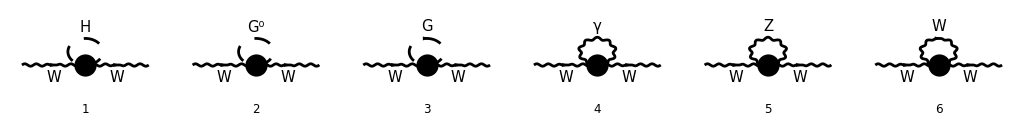

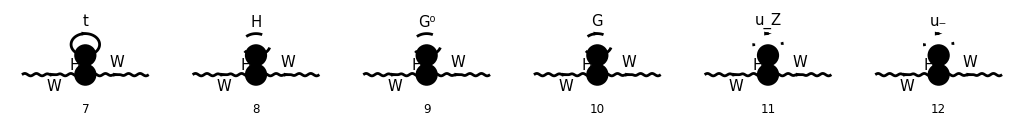

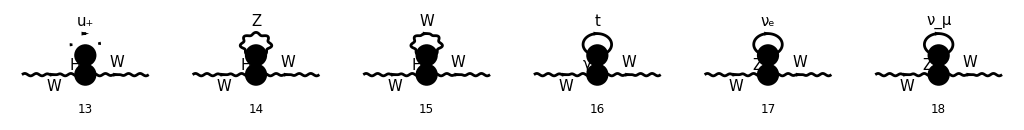

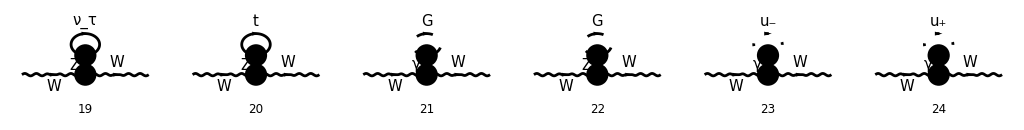

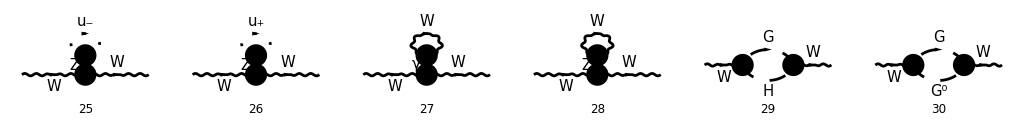

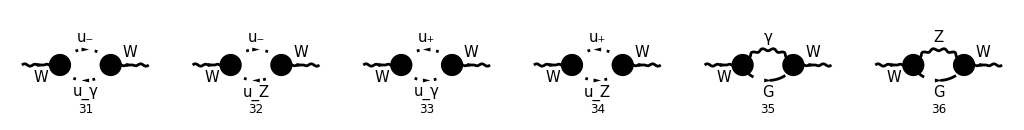

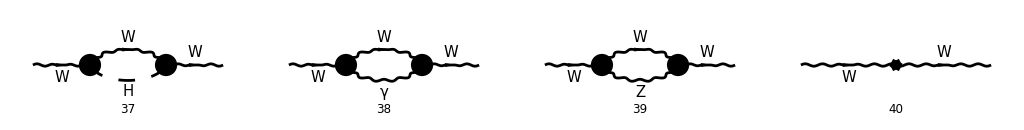

```mathematica
Paint[diag1[0],ColumnsXRows->{6,1},SheetHeader->None,Numbering->Simple,ImageSize->{1024,130}];
```

```mathematica
amp1[0]=FCFAConvert[CreateFeynAmp[diag1[0],Truncated->True,GaugeRules->{},PreFactor->1],IncomingMomenta->{p},OutgoingMomenta->{p},LorentzIndexNames->{mu, nu, rho, sigma},LoopMomenta->{l},UndoChiralSplittings->True,ChangeDimension->D,List->False,SMP->True,FinalSubstitutions->{dZW1-> dZW1/Epsilon, dMWsq1-> dMWsq1 SMP["m_Z"]^2/Epsilon,GaugeXi[S[1]]->GaugeXi, GaugeXi[W]-> GaugeXi, GaugeXi[g]-> GaugeXi, GaugeXi[Z]-> GaugeXi,FeynAmpDenominator[PropagatorDenominator[0,SMP["m_H"]]]-> -1/SMP["m_H"]^2}]
```

-g^murho g^nusigma (g^rhosigma/((l^2-ξ m_W^2).(l-p)^2)+((1-ξ_A) (l-p)^rho (p-l)^sigma)/((l^2-ξ m_W^2).((l-p)^2)^2)) m_W^2 e^2-(g^murho g^nusigma (g^rhosigma/((l^2-ξ m_W^2).((l-p)^2-m_Z^2))+((1-ξ) (l-p)^rho (p-l)^sigma)/((l^2-ξ m_W^2).((l-p)^2-m_Z^2).((l-p)^2-ξ m_Z^2))) m_W^2 (sin(θ_W))^2 e^2)/(cos(θ_W))^2-((l-p)^mu l^nu e^2)/(l^2.((l-p)^2-ξ m_W^2))+(l^mu (p-l)^nu e^2)/(l^2.((l-p)^2-ξ m_W^2))+(2 g^rhosigma (p^mu g^nurho+g^murho p^nu-2 g^munu p^rho) l^sigma e^2)/(0 (l^2-ξ m_W^2))+(g^Lor5Lor6/(0 (l^2-m_W^2))-((1-ξ) l^Lor5 l^Lor6)/((l^2-m_W^2).(l^2-ξ m_W^2) 0)) g^rhosigma (p^mu g^nurho+g^murho p^nu-2 g^munu p^rho) (-l^Lor5 g^Lor6sigma-g^Lor5sigma l^Lor6+2 g^Lor5Lor6 l^sigma) e^2-((-l-p)^Lor5 g^murho+g^Lor5rho (2 l-p)^mu+g^Lor5mu (2 p-l)^rho) ((g^Lor5Lor6 g^rhosigma)/(l^2.((l-p)^2-m_W^2))+((1-ξ) (l-p)^Lor5 (p-l)^Lor6 g^rhosigma)/(l^2.((l-p)^2-m_W^2).((l-p)^2-ξ m_W^2))-((1-ξ_A) g^Lor5Lor6 l^rho l^sigma)/((l^2)^2.((l-p)^2-m_W^2))-((1-ξ) (1-ξ_A) (l-p)^Lor5 (p-l)^Lor6 l^rho l^sigma)/((l^2)^2.((l-p)^2-m_W^2).((l-p)^2-ξ m_W^2))) ((l+p)^Lor6 g^nusigma+g^Lor6sigma (p-2 l)^nu+g^Lor6nu (l-2 p)^sigma) e^2-(g^rhosigma (p^mu g^nurho+g^murho p^nu-2 g^munu p^rho) l^sigma e^2 ((sin(θ_W))^2-(cos(θ_W))^2))/((0-m_Z^2) (l^2-ξ m_W^2) (sin(θ_W))^2)-((l-p)^mu l^nu (cos(θ_W))^2 e^2)/((l^2-ξ m_Z^2).((l-p)^2-ξ m_W^2) (sin(θ_W))^2)+(l^mu (p-l)^nu (cos(θ_W))^2 e^2)/((l^2-ξ m_Z^2).((l-p)^2-ξ m_W^2) (sin(θ_W))^2)+((g^Lor5Lor6/((0-m_Z^2) (l^2-m_W^2))-((1-ξ) l^Lor5 l^Lor6)/((l^2-m_W^2).(l^2-ξ m_W^2) (0-m_Z^2))) g^rhosigma (p^mu g^nurho+g^murho p^nu-2 g^munu p^rho) (-l^Lor5 g^Lor6sigma-g^Lor5sigma l^Lor6+2 g^Lor5Lor6 l^sigma) (cos(θ_W))^2 e^2)/(sin(θ_W))^2-1/(sin(θ_W))^2((-l-p)^Lor5 g^murho+g^Lor5rho (2 l-p)^mu+g^Lor5mu (2 p-l)^rho) (-((1-ξ)^2 (l-p)^Lor5 (p-l)^Lor6 l^rho l^sigma)/((l^2-m_Z^2).(l^2-ξ m_Z^2).((l-p)^2-m_W^2).((l-p)^2-ξ m_W^2))+((1-ξ) (l-p)^Lor5 (p-l)^Lor6 g^rhosigma)/((l^2-m_Z^2).((l-p)^2-m_W^2).((l-p)^2-ξ m_W^2))-((1-ξ) g^Lor5Lor6 l^rho l^sigma)/((l^2-m_Z^2).(l^2-ξ m_Z^2).((l-p)^2-m_W^2))+(g^Lor5Lor6 g^rhosigma)/((l^2-m_Z^2).((l-p)^2-m_W^2))) ((l+p)^Lor6 g^nusigma+g^Lor6sigma (p-2 l)^nu+g^Lor6nu (l-2 p)^sigma) (cos(θ_W))^2 e^2-(g^murho g^nusigma (g^rhosigma/((l^2-m_H^2).((l-p)^2-m_W^2))+((1-ξ) (l-p)^rho (p-l)^sigma)/((l^2-m_H^2).((l-p)^2-m_W^2).((l-p)^2-ξ m_W^2))) m_W^2 e^2)/(sin(θ_W))^2-(g^munu g^rhosigma (((1-ξ) l^rho l^sigma)/((l^2-m_W^2).(l^2-ξ m_W^2) m_H^2)-g^rhosigma/((l^2-m_W^2) m_H^2)) m_W^2 e^2)/(sin(θ_W))^2-(g^munu g^rhosigma (((1-ξ) l^rho l^sigma)/((l^2-m_Z^2).(l^2-ξ m_Z^2) m_H^2)-g^rhosigma/((l^2-m_Z^2) m_H^2)) m_W^2 e^2)/(2 (cos(θ_W))^2 (sin(θ_W))^2)-(ξ g^munu e^2 m_W^2)/((l^2-ξ m_W^2) m_H^2 (sin(θ_W))^2)+(g^munu e^2)/(2 (l^2-m_H^2) (sin(θ_W))^2)+((p-2 l)^mu (p-2 l)^nu e^2)/(4 (l^2-m_H^2).((l-p)^2-ξ m_W^2) (sin(θ_W))^2)+((p-2 l)^mu (p-2 l)^nu e^2)/(4 (l^2-ξ m_Z^2).((l-p)^2-ξ m_W^2) (sin(θ_W))^2)-(ξ g^munu e^2 m_W m_Z)/(2 (l^2-ξ m_Z^2) (cos(θ_W)) m_H^2 (sin(θ_W))^2)-(ⅈ tr((m_t-γ·l).(2/3 ⅈ γ^sigma e)) g^rhosigma (p^mu g^nurho+g^murho p^nu-2 g^munu p^rho) e SumOver(Col3,3))/(0 (l^2-m_t^2))+(ⅈ tr((m_t-γ·l).((2 ⅈ γ^sigma.(γ̄)^7 e (sin(θ_W)))/(3 (cos(θ_W)))-(ⅈ γ^sigma.(γ̄)^6 e (1/2-2/3 (sin(θ_W))^2))/((cos(θ_W)) (sin(θ_W))))) g^rhosigma (p^mu g^nurho+g^murho p^nu-2 g^munu p^rho) (cos(θ_W)) e SumOver(Col3,3))/((0-m_Z^2) (l^2-m_t^2) (sin(θ_W)))-(ⅈ tr((m_t-γ·l).(-(ⅈ e m_t)/(2 m_W (sin(θ_W))))) g^munu e m_W SumOver(Col3,3))/((l^2-m_t^2) m_H^2 (sin(θ_W)))+(3 ⅈ tr((-(γ·l)).(-(ⅈ γ^sigma.(γ̄)^6 e)/(2 (cos(θ_W)) (sin(θ_W))))) g^rhosigma (p^mu g^nurho+g^murho p^nu-2 g^munu p^rho) (cos(θ_W)) e)/(l^2 (0-m_Z^2) (sin(θ_W)))+(ⅈ dZW1 p^mu p^nu)/ε-(ⅈ dZW1 g^munu p^2)/ε-1/2 ⅈ (g^rhosigma/l^2-((1-ξ_A) l^rho l^sigma)/((l^2)^2)) (ⅈ g^musigma g^nurho e^2+ⅈ g^murho g^nusigma e^2-2 ⅈ g^munu g^rhosigma e^2)+ⅈ g^munu ((dZW1 m_W^2)/ε+(dMWsq1 m_Z^2)/ε)-ⅈ (g^rhosigma/(l^2-m_W^2)-((1-ξ) l^rho l^sigma)/((l^2-m_W^2).(l^2-ξ m_W^2))) (-(ⅈ g^musigma g^nurho e^2)/(sin(θ_W))^2+(2 ⅈ g^murho g^nusigma e^2)/(sin(θ_W))^2-(ⅈ g^munu g^rhosigma e^2)/(sin(θ_W))^2)-1/2 ⅈ (g^rhosigma/(l^2-m_Z^2)-((1-ξ) l^rho l^sigma)/((l^2-m_Z^2).(l^2-ξ m_Z^2))) ((ⅈ g^musigma g^nurho (cos(θ_W))^2 e^2)/(sin(θ_W))^2+(ⅈ g^murho g^nusigma (cos(θ_W))^2 e^2)/(sin(θ_W))^2-(2 ⅈ g^munu g^rhosigma (cos(θ_W))^2 e^2)/(sin(θ_W))^2)

```mathematica
amp1[1]=amp1[0]//SUNSimplify//DiracSimplify//TID[#,l,UsePaVeBasis->True,ToPaVe->True]&;
```

```mathematica
amp1[2] = amp1[1]//PaVeUVPart[#,Prefactor->1/(2 Pi)^D]&;
```

```mathematica
amp1[3] = FCReplaceD[amp1[2],D->4-2 Epsilon]//Series[#,{Epsilon,0,-1}]&//Normal//DiracSimplify//Simplify
```

1/(192 π^2 ε m_H^2 (cos(θ_W))^2 (sin(θ_W))^2)ⅈ (g^munu (3 ((cos(θ_W))^2 (e^2 (-8 m_t^4 SumOver(Col3,3)+m_H^2 (m_W^2 ((2 ξ_A+3 ξ^2-2 ξ+9) (sin(θ_W))^2-3 ξ^2+ξ-12)+ξ m_Z^2)+3 m_H^4+12 m_W^4)+64 π^2 m_H^2 (sin(θ_W))^2 (dMWsq1 m_Z^2+dZW1 m_W^2))+e^2 m_H^2 (cos(θ_W))^4 ((3 ξ^2+ξ+12) m_W^2+(ξ+3) m_Z^2)-2 e^2 ξ^2 m_W m_Z^3 (cos(θ_W))+e^2 m_W^2 (2 (ξ^2+3) m_Z^2-(ξ+3) m_H^2 (sin(θ_W))^4))-2 p^2 m_H^2 (cos(θ_W))^2 (e^2 ((3 ξ_A+3 ξ-26) (sin(θ_W))^2+(6 ξ-26) (cos(θ_W))^2+1)+96 π^2 dZW1 (sin(θ_W))^2))+2 m_H^2 p^mu p^nu (cos(θ_W))^2 (e^2 ((3 ξ_A+3 ξ-26) (sin(θ_W))^2+(6 ξ-26) (cos(θ_W))^2+1)+96 π^2 dZW1 (sin(θ_W))^2))

```mathematica
amp1[3]=amp1[3]/.{SumOver[__, 3]-> Nc}
```

1/(192 π^2 ε m_H^2 (cos(θ_W))^2 (sin(θ_W))^2)ⅈ (g^munu (3 ((cos(θ_W))^2 (e^2 (m_H^2 (m_W^2 ((2 ξ_A+3 ξ^2-2 ξ+9) (sin(θ_W))^2-3 ξ^2+ξ-12)+ξ m_Z^2)+3 m_H^4-8 Nc m_t^4+12 m_W^4)+64 π^2 m_H^2 (sin(θ_W))^2 (dMWsq1 m_Z^2+dZW1 m_W^2))+e^2 m_H^2 (cos(θ_W))^4 ((3 ξ^2+ξ+12) m_W^2+(ξ+3) m_Z^2)-2 e^2 ξ^2 m_W m_Z^3 (cos(θ_W))+e^2 m_W^2 (2 (ξ^2+3) m_Z^2-(ξ+3) m_H^2 (sin(θ_W))^4))-2 p^2 m_H^2 (cos(θ_W))^2 (e^2 ((3 ξ_A+3 ξ-26) (sin(θ_W))^2+(6 ξ-26) (cos(θ_W))^2+1)+96 π^2 dZW1 (sin(θ_W))^2))+2 m_H^2 p^mu p^nu (cos(θ_W))^2 (e^2 ((3 ξ_A+3 ξ-26) (sin(θ_W))^2+(6 ξ-26) (cos(θ_W))^2+1)+96 π^2 dZW1 (sin(θ_W))^2))

```mathematica
pTerms=SelectNotFree2[amp1[3], p]
```

(ⅈ p^mu p^nu (e^2 ((3 ξ_A+3 ξ-26) (sin(θ_W))^2+(6 ξ-26) (cos(θ_W))^2+1)+96 π^2 dZW1 (sin(θ_W))^2))/(96 π^2 ε (sin(θ_W))^2)-(ⅈ p^2 g^munu (e^2 ((3 ξ_A+3 ξ-26) (sin(θ_W))^2+(6 ξ-26) (cos(θ_W))^2+1)+96 π^2 dZW1 (sin(θ_W))^2))/(96 π^2 ε (sin(θ_W))^2)

```mathematica
mTerms =SelectFree2[amp1[3], p]
```

1/(64 π^2 ε m_H^2 (cos(θ_W))^2 (sin(θ_W))^2)ⅈ g^munu ((cos(θ_W))^2 (e^2 (m_H^2 (m_W^2 ((2 ξ_A+3 ξ^2-2 ξ+9) (sin(θ_W))^2-3 ξ^2+ξ-12)+ξ m_Z^2)+3 m_H^4-8 Nc m_t^4+12 m_W^4)+64 π^2 m_H^2 (sin(θ_W))^2 (dMWsq1 m_Z^2+dZW1 m_W^2))+e^2 m_H^2 (cos(θ_W))^4 ((3 ξ^2+ξ+12) m_W^2+(ξ+3) m_Z^2)-2 e^2 ξ^2 m_W m_Z^3 (cos(θ_W))+e^2 m_W^2 (2 (ξ^2+3) m_Z^2-(ξ+3) m_H^2 (sin(θ_W))^4))

```mathematica
dZW1replace={dZW1-> Collect[Normal[Simplify[dZW1/.Solve[pTerms==0, dZW1][[1]]/.{SMP["Delta"]->1/Epsilon}/.{SumOver[__, 3]-> Nc,SMP["m_t"]-> Y*v/√2, SMP["m_W"]-> v/2 g2, SMP["m_Z"]-> v/2 √(g2^2 + gY^2), SMP["e"]-> g2*SMP["sin_W"], SMP["cos_W"]-> g2/(√(g2^2 + gY^2)), SMP["m_H"]-> √(2 λ) v}]],{gY, g2, Y},Simplify]}
```

{dZW1→-(g2^2 ((3 ξ_A+3 ξ-26) (g2^2+gY^2) (sin(θ_W))^2+g2^2 (6 ξ-25)+gY^2))/(96 π^2 (g2^2+gY^2))}

```mathematica
dMWsqreplace={dMWsq1-> Collect[Normal[Simplify[dMWsq1/.Solve[mTerms==0, dMWsq1][[1]]/.dZW1replace/.{SMP["Delta"]->1/Epsilon}//.{SumOver[__, 3]-> Nc,SMP["m_t"]-> Y*v/√2, SMP["m_W"]-> v/2 g2, SMP["m_Z"]-> v/2 √(g2^2 + gY^2), SMP["e"]-> g2*SMP["sin_W"], SMP["cos_W"]-> g2/(√(g2^2 + gY^2)),SMP["sin_W"]-> gY/(√(g2^2 + gY^2)), SMP["m_H"]-> √(2 λ) v}]],{gY, g2, Y, λ},Simplify]}
```

{dMWsq1→-(g2^2 (2 g2^2 (9 gY^2+118 λ)+27 g2^4-36 gY^2 λ+9 gY^4+288 λ^2-48 Nc Y^4))/(768 π^2 λ (g2^2+gY^2))}

```mathematica
dMWsq1-dMZsq1/.dMWsqreplace/.dMZsqreplace//Simplify
```

(9 g2^4 (27 gY^2-8 λ (Nc+3))+6 g2^2 (2 gY^2 λ (4 Nc-117)+27 gY^4+72 λ Nc Y^2)-68 gY^4 λ (2 Nc+9)+432 gY^2 (6 λ^2+λ Nc Y^2-Nc Y^4)+81 gY^6)/(6912 π^2 λ (g2^2+gY^2))

### g2 Renormalization

```mathematica
{diagWVertex,diagWVertexCT}=InsertFields[#,{V[3]}->{F[2,{1}],-F[1,{1}]},Sequence@@params, ExcludeParticles->{F[3|4,{1|2}],F[4,{3}], F[2]}]&/@{topVertex[1,2],topVertexCT[1,2]};
```

```mathematica
diag1[0]=diagZVertex[[0]][Sequence@@diagWVertex,Sequence@@diagWVertexCT];
```

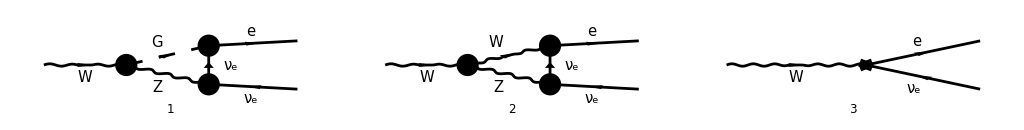

```mathematica
Paint[diag1[0],ColumnsXRows->{6,1},SheetHeader->None,Numbering->Simple,ImageSize->{1024,130}];
```

```mathematica
amp1[0]=FCFAConvert[CreateFeynAmp[diag1[0],Truncated->True,GaugeRules->{},PreFactor->1],IncomingMomenta->{p},OutgoingMomenta->{p1, p2},LorentzIndexNames->{mu, nu, rho, sigma},LoopMomenta->{l},UndoChiralSplittings->True,ChangeDimension->D,List->False,SMP->True,FinalSubstitutions->{dZZZ1-> dZZZ1/Epsilon, dMZsq1-> dMZsq1 SMP["m_Z"]^2/Epsilon,GaugeXi[S[1]]->GaugeXi, GaugeXi[W]-> GaugeXi, GaugeXi[g]-> GaugeXi, GaugeXi[Z]-> GaugeXi,FeynAmpDenominator[PropagatorDenominator[0,SMP["m_H"]]]-> -1/SMP["m_H"]^2}]
```

-(ⅈ e γ^mu.(γ̄)^7 (1/2 Conjugate[dZfL1(2,1,1)]+1/2 dZfL1(1,1,1)-dSW1/(sin(θ_W))+dZe1+dZW1/2))/(√2 (sin(θ_W)))-(e m_W g^munu (sin(θ_W)) (-(ⅈ e (γ̄)^7 m_e)/(√2 m_W (sin(θ_W)))).(γ·(p1-l)).(ⅈ e γ^rho.(γ̄)^7)/(2 (cos(θ_W)) (sin(θ_W))) (g^nurho/((l^2-ξ m_W^2).(l-p1)^2.((l-p1-p2)^2-m_Z^2))+((1-ξ) (l-p1-p2)^nu (-l+p1+p2)^rho)/((l^2-ξ m_W^2).(l-p1)^2.((l-p1-p2)^2-m_Z^2).((l-p1-p2)^2-ξ m_Z^2))))/(cos(θ_W))+1/(sin(θ_W))e (cos(θ_W)) (g^musigma (-l+p+p1+p2)^nu+g^munu (-l-p)^sigma+g^nusigma (2 l-p1-p2)^mu) (ⅈ e γ^rho.(γ̄)^7)/(√2 (sin(θ_W))).(γ·(p1-l)).(ⅈ e γ^Lor5.(γ̄)^7)/(2 (cos(θ_W)) (sin(θ_W))) (-((1-ξ) l^nu l^rho g^Lor5sigma)/((l^2-m_W^2).(l^2-ξ m_W^2).(l-p1)^2.((l-p1-p2)^2-m_Z^2))+((1-ξ) g^nurho (-l+p1+p2)^Lor5 (l-p1-p2)^sigma)/((l^2-m_W^2).(l-p1)^2.((l-p1-p2)^2-m_Z^2).((l-p1-p2)^2-ξ m_Z^2))+(g^Lor5sigma g^nurho)/((l^2-m_W^2).(l-p1)^2.((l-p1-p2)^2-m_Z^2))+-((1-ξ)^2 l^nu l^rho (-l+p1+p2)^Lor5 (l-p1-p2)^sigma)/((l^2-m_W^2).(l^2-ξ m_W^2).(l-p1)^2.((l-p1-p2)^2-m_Z^2).((l-p1-p2)^2-ξ m_Z^2)))

```mathematica
amp1[1]=amp1[0]//SUNSimplify//DiracSimplify//TID[#,l,UsePaVeBasis->True,ToPaVe->True]&;
```

```mathematica
amp1[2] = amp1[1]//PaVeUVPart[#,Prefactor->1/(2 Pi)^D]&;
```

```mathematica
amp1[3] = FCReplaceD[amp1[2],D->4-2 Epsilon]//Series[#,{Epsilon,0,-1}]&//Normal//DiracSimplify//Simplify
```

(ⅈ e^3 SumOver(Col4,3) (16 (sin(θ_W))^4-12 (sin(θ_W))^2+3) (tr(γ^rho.γ^nu.(γ·p1).γ^mu.(γ̄)^5)-tr(γ^rho.(γ·p1).γ^nu.γ^mu.(γ̄)^5)+tr((γ·p1).γ^nu.γ^rho.γ^mu.(γ̄)^5)-tr((γ·p1).γ^rho.γ^nu.γ^mu.(γ̄)^5)+tr(γ^rho.γ^nu.(γ·p2).γ^mu.(γ̄)^5)-tr((γ·p2).γ^rho.γ^nu.γ^mu.(γ̄)^5)))/(768 π^2 ε (cos(θ_W))^3 (sin(θ_W))^3)

## QCD Renormaliztion

```mathematica
MakeBoxes[mu,TraditionalForm]:="μ";
MakeBoxes[nu,TraditionalForm]:="ν";
MakeBoxes[rho,TraditionalForm]:="ρ";
MakeBoxes[si,TraditionalForm]:="σ";

params={InsertionLevel->{Particles},Model->FileNameJoin[{"QCD", "QCD"}],GenericModel->FileNameJoin[{"QCD", "QCD"}],ExcludeParticles->{F[3|4,{2|3}],F[4,{1}]}};
top[i_,j_]:=CreateTopologies[1,i->j,ExcludeTopologies->{Tadpoles,WFCorrections,WFCorrectionCTs}];
topTriangle[i_,j_]:=CreateTopologies[1,i->j,ExcludeTopologies->{Tadpoles,WFCorrections,WFCorrectionCTs,SelfEnergies}];
```

```mathematica
topCT[i_,j_]:=CreateCTTopologies[1,i->j,ExcludeTopologies->{Tadpoles,WFCorrections,WFCorrectionCTs}];
topTriangleCT[i_,j_]:=CreateCTTopologies[1,i->j,ExcludeTopologies->{Tadpoles,WFCorrections,WFCorrectionCTs,SelfEnergyCTs}];
```

```mathematica
{diagQuarkSE,diagQuarkSECT}=InsertFields[#,{F[3,{1}]}->{F[3,{1}]},Sequence@@params]&/@{top[1,1],topCT[1,1]};

{diagGluonSE,diagGluonSECT}=InsertFields[#,{V[5]}->{V[5]},Sequence@@params]&/@{top[1,1],topCT[1,1]};

{diagGhostSE,diagGhostSECT}=InsertFields[#,{U[5]}->{U[5]},Sequence@@params]&/@{top[1,1],topCT[1,1]};

{diagQuarkGluonVertex,diagQuarkGluonVertexCT}=InsertFields[#,{F[3,{1}],V[5]}->{F[3,{1}]},Sequence@@params]&/@{topTriangle[2,1],topTriangleCT[2,1]};
```

```mathematica
diag1[0]=diagQuarkSE[[0]][Sequence@@diagQuarkSE,Sequence@@diagQuarkSECT];
diag2[0]=diagGluonSE[[0]][Sequence@@diagGluonSE,Sequence@@diagGluonSECT];
diag3[0]=diagGhostSE[[0]][Sequence@@diagGhostSE,Sequence@@diagGhostSECT];
diag4[0]=diagQuarkGluonVertex[[0]][Sequence@@diagQuarkGluonVertex,Sequence@@diagQuarkGluonVertexCT];
```

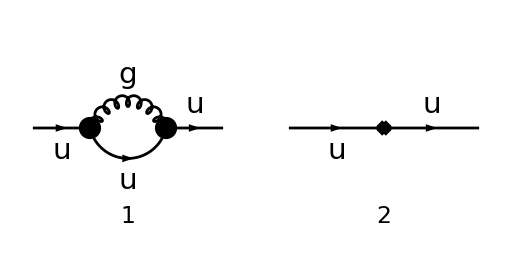

```mathematica
Paint[diag1[0],ColumnsXRows->{2,1},SheetHeader->None,Numbering->Simple,ImageSize->{512,256}];
```

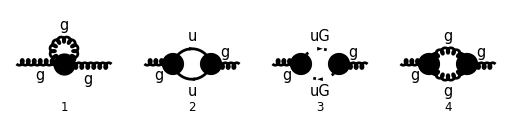

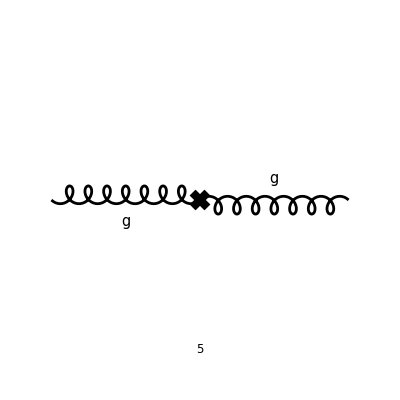

```mathematica
Paint[diag2[0],ColumnsXRows->{4,1},SheetHeader->None,Numbering->Simple,ImageSize->{512,128}];
```

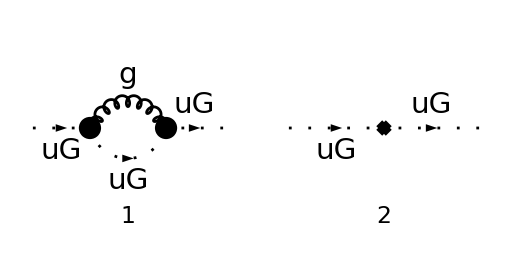

```mathematica
Paint[diag3[0],ColumnsXRows->{2,1},SheetHeader->None,Numbering->Simple,ImageSize->{512,256}];
```

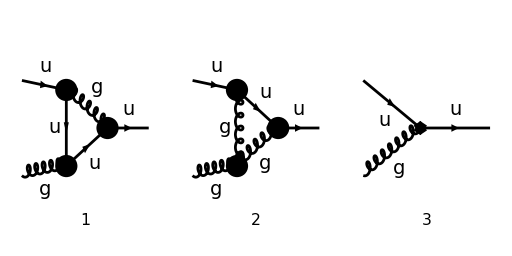

```mathematica
Paint[diag4[0],ColumnsXRows->{3,1},SheetHeader->None,Numbering->Simple,ImageSize->{512,256}];
```

Quark self energy

```mathematica
ampQuarkSE[0]=FCFAConvert[CreateFeynAmp[diag1[0],Truncated->True,GaugeRules->{},PreFactor->1],IncomingMomenta->{p},OutgoingMomenta->{p},LorentzIndexNames->{mu,nu},DropSumOver->True,LoopMomenta->{l},UndoChiralSplittings->True,ChangeDimension->D,List->False,SMP->True,FinalSubstitutions->{Zm->SMP["Z_m"],Zpsi->SMP["Z_psi"],SMP["m_u"]->0}]
```

(((1-ξ_G) (l-p)^μ (p-l)^ν)/(l^2.((l-p)^2)^2)+g^μν/(l^2.(l-p)^2)) (-ⅈ γ^ν g_s T_Col2Col3^Glu3).(γ·l).(-ⅈ γ^μ g_s T_Col3Col1^Glu3)+ⅈ (Z_ψ-1) δ_Col1Col2 γ·p

Gluon self energy

```mathematica
ampGluonSE[0]=FCFAConvert[CreateFeynAmp[diag2[0],Truncated->True,GaugeRules->{},PreFactor->1],IncomingMomenta->{p},OutgoingMomenta->{p},LorentzIndexNames->{mu,nu,rho,si},DropSumOver->True,LoopMomenta->{l},UndoChiralSplittings->True,ChangeDimension->D,List->True,SMP->True,FinalSubstitutions->{ZA->SMP["Z_A"],Zxi->SMP["Z_xi"],SMP["m_u"]->0}]
```

{-1/2 ⅈ (g^ρσ/l^2-((1-ξ_G) l^ρ l^σ)/((l^2)^2)) (ⅈ g^μρ g^νσ f^Glu1Glu3$AL$15081 f^Glu2Glu3$AL$15081 g_s^2-2 ⅈ g^μν g^ρσ f^Glu1Glu3$AL$15082 f^Glu2Glu3$AL$15082 g_s^2+ⅈ g^μσ g^νρ f^Glu1Glu3$AL$15084 f^Glu2Glu3$AL$15084 g_s^2),(tr((-(γ·l)).(-ⅈ γ^ν g_s T_Col3Col4^Glu2).(γ·(p-l)).(-ⅈ γ^μ g_s T_Col4Col3^Glu1)))/(l^2.(l-p)^2),-((l-p)^μ l^ν g_s^2 f^Glu1Glu3Glu4 f^Glu2Glu3Glu4)/(l^2.(l-p)^2),-1/2 (-((1-ξ_G)^2 (l-p)^Lor5 (p-l)^Lor6 l^ρ l^σ)/((l^2)^2.((l-p)^2)^2)+((1-ξ_G) (l-p)^Lor5 (p-l)^Lor6 g^ρσ)/(l^2.((l-p)^2)^2)-((1-ξ_G) g^Lor5Lor6 l^ρ l^σ)/((l^2)^2.(l-p)^2)+(g^Lor5Lor6 g^ρσ)/(l^2.(l-p)^2)) (-l^Lor5 g^μρ g_s f^Glu1Glu3Glu4-p^Lor5 g^μρ g_s f^Glu1Glu3Glu4+g^Lor5ρ l^μ g_s f^Glu1Glu3Glu4+g^Lor5ρ (l-p)^μ g_s f^Glu1Glu3Glu4+g^Lor5μ p^ρ g_s f^Glu1Glu3Glu4+g^Lor5μ (p-l)^ρ g_s f^Glu1Glu3Glu4) (l^Lor6 g^νσ g_s f^Glu2Glu3Glu4+p^Lor6 g^νσ g_s f^Glu2Glu3Glu4-g^Lor6σ l^ν g_s f^Glu2Glu3Glu4+g^Lor6σ (p-l)^ν g_s f^Glu2Glu3Glu4+g^Lor6ν (l-p)^σ g_s f^Glu2Glu3Glu4-g^Lor6ν p^σ g_s f^Glu2Glu3Glu4),ⅈ p^μ p^ν (Z_A-1) δ^Glu1Glu2-ⅈ g^μν p^2 (Z_A-1) δ^Glu1Glu2-(ⅈ p^μ p^ν (Z_A-Z_ξ) δ^Glu1Glu2)/(ξ_G Z_ξ)}

Ghost self energy

```mathematica
ampGhostSE[0]=FCFAConvert[CreateFeynAmp[diag3[0],Truncated->True,GaugeRules->{},PreFactor->1],IncomingMomenta->{p},OutgoingMomenta->{p},LorentzIndexNames->{mu,nu},DropSumOver->True,LoopMomenta->{l},UndoChiralSplittings->True,ChangeDimension->D,List->False,SMP->True,FinalSubstitutions->{Zu->SMP["Z_u"]}]
```

-g_s^2 l^μ p^ν f^Glu1Glu3Glu4 f^Glu2Glu3Glu4 (((1-ξ_G) (l-p)^μ (p-l)^ν)/(l^2.((l-p)^2)^2)+g^μν/(l^2.(l-p)^2))+ⅈ p^2 (Z_u-1) δ^Glu1Glu2

Quark Gluon vertex

```mathematica
ampQGlVertex[0]=FCFAConvert[CreateFeynAmp[diag4[0],Truncated->True,GaugeRules->{},PreFactor->1],IncomingMomenta->{p1,k},OutgoingMomenta->{p2},LorentzIndexNames->{mu,nu,rho},DropSumOver->True,LoopMomenta->{l},UndoChiralSplittings->True,ChangeDimension->D,List->False,SMP->True,FinalSubstitutions->{ZA->SMP["Z_A"],Zg->SMP["Z_g"],Zpsi->SMP["Z_psi"],SMP["m_u"]->0}]
```

ⅈ (((1-ξ_G) (k+l-p2)^ν (-k-l+p2)^ρ)/(l^2.(k+l)^2.((k+l-p2)^2)^2)+g^νρ/(l^2.(k+l)^2.(k+l-p2)^2)) (-ⅈ γ^ρ g_s T_Col3Col5^Glu4).(γ·(k+l)).(-ⅈ γ^μ g_s T_Col5Col4^Glu2).(γ·l).(-ⅈ γ^ν g_s T_Col4Col1^Glu4)-ⅈ (g_s g^Lor4ρ (-k-l)^μ f^Glu2Glu4Glu5+g_s g^Lor4μ (k+l)^ρ f^Glu2Glu4Glu5+g_s (-k^Lor4) g^μρ f^Glu2Glu4Glu5+g_s k^ρ g^Lor4μ f^Glu2Glu4Glu5+g_s l^Lor4 g^μρ f^Glu2Glu4Glu5-g_s l^μ g^Lor4ρ f^Glu2Glu4Glu5) (((1-ξ_G) g^νρ (-k-l)^Lor4 (k+l)^Lor5)/(l^2.((k+l)^2)^2.(k+l-p2)^2)-((1-ξ_G) l^ν l^ρ g^Lor4Lor5)/((l^2)^2.(k+l)^2.(k+l-p2)^2)+-((1-ξ_G)^2 l^ν l^ρ (-k-l)^Lor4 (k+l)^Lor5)/((l^2)^2.((k+l)^2)^2.(k+l-p2)^2)+(g^Lor4Lor5 g^νρ)/(l^2.(k+l)^2.(k+l-p2)^2)) (-ⅈ g_s γ^Lor5 T_Col3Col4^Glu5).(γ·(-k-l+p2)).(-ⅈ γ^ν g_s T_Col4Col1^Glu4)-ⅈ γ^μ g_s (√Z_A Z_g Z_ψ-1) T_Col3Col1^Glu2

### Quark Self-Energy

```mathematica
ampQuarkSE[1]=ampQuarkSE[0]//SUNSimplify//DiracSimplify//TID[#,l,UsePaVeBasis->True,ToPaVe->True]&
```

1/4 ⅈ π^2 (1-C_A^2) g_s^2 (C_A-2 C_F) δ_Col1Col2 (-D-2 ξ_G+4) γ·p B_0(p^2,0,0)+1/2 ⅈ π^2 p^2 (1-C_A^2) (1-ξ_G) g_s^2 (C_A-2 C_F) δ_Col1Col2 γ·p C_1(p^2,p^2,0,0,0,0)-ⅈ C_A (1-Z_ψ) (C_A-2 C_F) δ_Col1Col2 γ·p

```mathematica
ampQuarkSEDiv[0]=ampQuarkSE[1]//PaVeUVPart[#,Prefactor->1/(2 Pi)^D]&
```

(ⅈ (2 π)^-D (C_A-2 C_F) δ_Col1Col2 γ·p (-2^(D+2) π^D C_A Z_ψ+D (2 π)^D C_A Z_ψ+2^(D+2) π^D C_A-D (2 π)^D C_A+π^2 (-C_A^2) ξ_G g_s^2+π^2 ξ_G g_s^2))/(D-4)

```mathematica
ampQuarkSEDiv[1]=FCReplaceD[ampQuarkSEDiv[0],D->4-2 Epsilon]//Series[#,{Epsilon,0,0}]&//Normal//FCHideEpsilon//Simplify
```

(ⅈ (C_A-2 C_F) δ_Col1Col2 γ·p ((C_A^2-1) (Δ+ℽ+log(π)) ξ_G g_s^2+32 π^2 C_A (Z_ψ-1)))/(32 π^2)

```mathematica
ampQuarkSEDiv[2]=ampQuarkSEDiv[1]//ReplaceRepeated[#,{SMP["Z_m"]->1+alpha SMP["d_m"],SMP["Z_psi"]->1+alpha SMP["d_psi"]}]&//Series[#,{alpha,0,1}]&//Normal//ReplaceAll[#,alpha->1]&//SelectNotFree2[#,SMP["Delta"],SMP["d_m"],SMP["d_psi"]]&
```

(ⅈ Δ (C_A^2-1) ξ_G g_s^2 (C_A-2 C_F) δ_Col1Col2 γ·p)/(32 π^2)+ⅈ C_A δ_ψ (C_A-2 C_F) δ_Col1Col2 γ·p

```mathematica
ampQuarkSEDiv[3]=ampQuarkSEDiv[2]//SUNSimplify//Collect2[#,DiracGamma,Factoring->Simplify]&
```

(ⅈ (C_A-2 C_F) δ_Col1Col2 γ·p (32 π^2 C_A δ_ψ+Δ (C_A^2-1) ξ_G g_s^2))/(32 π^2)

```mathematica
sol[1]=Solve[ampQuarkSEDiv[3]==0,SMP["d_psi"]]//Flatten//ReplaceAll[#,Rule[a_,b_]:>Rule[a,SUNSimplify[b]]]&//ReplaceAll[#,SMP["g_s"]^2->4 Pi SMP["alpha_s"]]&;

solMS1=sol[1]/. {SMP["d_psi"]->SMP["d_psi^MS"],SMP["Delta"]->1/Epsilon}
```

{δ_ψ^MS→-(C_F ξ_G α_s)/(4 π ε)}

### Gluon Self-Energy

```mathematica
ampGluonSE[1]=(ampGluonSE[0][[1]]+Nf ampGluonSE[0][[2]]+Total[ampGluonSE[0][[3;;]]])//SUNSimplify//DiracSimplify;
```

```mathematica
ampGluonSE[2]=TID[ampGluonSE[1],l,UsePaVeBasis->True,ToPaVe->True];
```

```mathematica
ampGluonSEDiv[0]=ampGluonSE[2]//PaVeUVPart[#,Prefactor->1/(2 Pi)^D]&
```

1/((D-4) (D-1) ξ_G Z_ξ)ⅈ 2^(-D-1) π^-D (4 C_A π^2 p^μ p^ν g_s^2 Z_ξ ξ_G^3-C_A D π^2 p^μ p^ν g_s^2 Z_ξ ξ_G^3-14 C_A π^2 p^μ p^ν g_s^2 Z_ξ ξ_G^2+2 C_A D π^2 p^μ p^ν g_s^2 Z_ξ ξ_G^2-2 C_A π^2 g^μν p^2 g_s^2 Z_ξ ξ_G^2+2 C_A D π^2 g^μν p^2 g_s^2 Z_ξ ξ_G^2+30 C_A π^2 p^μ p^ν g_s^2 Z_ξ ξ_G-C_A D π^2 p^μ p^ν g_s^2 Z_ξ ξ_G-8 N_f π^2 p^μ p^ν g_s^2 Z_ξ ξ_G-18 C_A π^2 g^μν p^2 g_s^2 Z_ξ ξ_G-2 C_A D π^2 g^μν p^2 g_s^2 Z_ξ ξ_G+8 N_f π^2 g^μν p^2 g_s^2 Z_ξ ξ_G-2^(D+3) π^D p^μ p^ν Z_ξ ξ_G-2^(D+1) D^2 π^D p^μ p^ν Z_ξ ξ_G+5 2^(D+1) D π^D p^μ p^ν Z_ξ ξ_G+2^(D+3) π^D g^μν p^2 Z_ξ ξ_G+2^(D+1) D^2 π^D g^μν p^2 Z_ξ ξ_G-5 2^(D+1) D π^D g^μν p^2 Z_ξ ξ_G+2^(D+3) π^D p^μ p^ν Z_A Z_ξ ξ_G+2^(D+1) D^2 π^D p^μ p^ν Z_A Z_ξ ξ_G-5 2^(D+1) D π^D p^μ p^ν Z_A Z_ξ ξ_G-2^(D+3) π^D g^μν p^2 Z_A Z_ξ ξ_G-2^(D+1) D^2 π^D g^μν p^2 Z_A Z_ξ ξ_G+5 2^(D+1) D π^D g^μν p^2 Z_A Z_ξ ξ_G-2^(D+3) π^D p^μ p^ν Z_A-2^(D+1) D^2 π^D p^μ p^ν Z_A+5 2^(D+1) D π^D p^μ p^ν Z_A+2^(D+3) π^D p^μ p^ν Z_ξ+2^(D+1) D^2 π^D p^μ p^ν Z_ξ-5 2^(D+1) D π^D p^μ p^ν Z_ξ) δ^Glu1Glu2

```mathematica
ampGluonSEDiv[1]=FCReplaceD[ampGluonSEDiv[0],D->4-2 Epsilon]//Series[#,{Epsilon,0,0}]&//Normal//FCHideEpsilon//SUNSimplify;

ampGluonSEDiv[2]=ampGluonSEDiv[1]//ReplaceRepeated[#,{SMP["Z_A"]->1+alpha SMP["d_A"],SMP["Z_xi"]->1+alpha SMP["d_A"]}]&//Series[#,{alpha,0,1}]&//Normal//ReplaceAll[#,alpha->1]&//SelectNotFree2[#,SMP["Delta"],SMP["d_A"],SMP["d_xi"]]&
```

(ⅈ Δ C_A ξ_G g_s^2 p^μ p^ν δ^Glu1Glu2)/(32 π^2)-(ⅈ Δ p^2 C_A ξ_G g_s^2 g^μν δ^Glu1Glu2)/(32 π^2)-(13 ⅈ Δ C_A g_s^2 p^μ p^ν δ^Glu1Glu2)/(96 π^2)+(13 ⅈ Δ p^2 C_A g_s^2 g^μν δ^Glu1Glu2)/(96 π^2)-ⅈ p^2 δ_A g^μν δ^Glu1Glu2+ⅈ δ_A p^μ p^ν δ^Glu1Glu2+(ⅈ Δ N_f g_s^2 p^μ p^ν δ^Glu1Glu2)/(24 π^2)-(ⅈ Δ p^2 N_f g_s^2 g^μν δ^Glu1Glu2)/(24 π^2)

```mathematica
sol[3]=Solve[ampGluonSEDiv[2]==0,SMP["d_A"]]//Flatten//ReplaceAll[#,SMP["g_s"]^2->4 Pi SMP["alpha_s"]]&//Simplify;
solMS2=sol[3]/. {SMP["d_A"]->SMP["d_A^MS"],SMP["Delta"]->1/Epsilon}
```

{δ_A^MS→-(α_s (3 C_A ξ_G-13 C_A+4 N_f))/(24 π ε)}

### Ghost Self-Energy

```mathematica
ampGhostSE[1]=ampGhostSE[0]//SUNSimplify//DiracSimplify;

ampGhostSE[2]=TID[ampGhostSE[1],l,UsePaVeBasis->True,ToPaVe->True];
```

```mathematica
ampGhostSEDiv[0]=ampGhostSE[2]//PaVeUVPart[#,Prefactor->1/(2 Pi)^D]&
```

(ⅈ 2^(-D-1) π^-D p^2 δ^Glu1Glu2 (π^2 (-C_A) ξ_G g_s^2+3 π^2 C_A g_s^2-2^(D+3) π^D Z_u+2^(D+1) D π^D Z_u+2^(D+3) π^D-2^(D+1) D π^D))/(D-4)

```mathematica
ampGhostSEDiv[1]=FCReplaceD[ampGhostSEDiv[0],D->4-2 Epsilon]//Series[#,{Epsilon,0,0}]&//Normal//FCHideEpsilon//SUNSimplify
```

-(ⅈ p^2 δ^Glu1Glu2 (-Δ C_A ξ_G g_s^2+ℽ (-C_A) ξ_G g_s^2+log(4 π) C_A ξ_G g_s^2-2 log(π) C_A ξ_G g_s^2-2 log(2) C_A ξ_G g_s^2+3 Δ C_A g_s^2+3 ℽ C_A g_s^2-3 log(4 π) C_A g_s^2+6 log(π) C_A g_s^2+6 log(2) C_A g_s^2-64 π^2 Z_u+64 π^2))/(64 π^2)

```mathematica
ampGhostSEDiv[2]=ampGhostSEDiv[1]//ReplaceRepeated[#,{SMP["Z_u"]->1+alpha SMP["d_u"]}]&//Series[#,{alpha,0,1}]&//Normal//ReplaceAll[#,alpha->1]&//SelectNotFree2[#,SMP["Delta"],SMP["d_u"]]&//Simplify
```

(ⅈ p^2 δ^Glu1Glu2 (Δ C_A (ξ_G-3) g_s^2+64 π^2 δ_u))/(64 π^2)

```mathematica
sol[4]=Solve[ampGhostSEDiv[2]==0,SMP["d_u"]]//Flatten//ReplaceAll[#,SMP["g_s"]^2->4 Pi SMP["alpha_s"]]&//Simplify;
solMS3=sol[4]/. {SMP["d_u"]->SMP["d_u^MS"],SMP["Delta"]->1/Epsilon}
```

{δ_u^MS→-(C_A (ξ_G-3) α_s)/(16 π ε)}

### Quark-Gluon Vertex

```mathematica
ampQGlVertex[1]=ampQGlVertex[0]//SUNSimplify//DiracSimplify;

ampQGlVertex[2]=TID[ampQGlVertex[1],l,UsePaVeBasis->True,ToPaVe->True];
```

```mathematica
ampQGlVertexDiv[0]=ampQGlVertex[2]//PaVeUVPart[#,Prefactor->1/(2 Pi)^D]&
```

-1/(D-4)ⅈ (2 π)^-D (-2^(D+3) π^D C_A γ^μ C_F g_s T_Col3Col1^Glu2+2^(D+1) D π^D C_A γ^μ C_F g_s T_Col3Col1^Glu2+2^(D+3) π^D C_A √Z_A γ^μ C_F g_s Z_g Z_ψ T_Col3Col1^Glu2-2^(D+1) D π^D C_A √Z_A γ^μ C_F g_s Z_g Z_ψ T_Col3Col1^Glu2+2^(D+2) π^D C_A^2 γ^μ g_s T_Col3Col1^Glu2-D (2 π)^D C_A^2 γ^μ g_s T_Col3Col1^Glu2-2^(D+2) π^D C_A^2 √Z_A γ^μ g_s Z_g Z_ψ T_Col3Col1^Glu2+D (2 π)^D C_A^2 √Z_A γ^μ g_s Z_g Z_ψ T_Col3Col1^Glu2+π^2 C_A γ^μ ξ_G g_s^3 T_Col3Col1^Glu2-2 π^2 γ^μ C_F ξ_G g_s^3 T_Col3Col1^Glu2-3 ⅈ π^2 γ^μ ξ_G g_s^3 f^(Glu2FCGV(sun12491)FCGV(sun12492)) (T^(FCGV(sun12492))T^(FCGV(sun12491)))_Col3Col1-3 ⅈ π^2 γ^μ g_s^3 f^(Glu2FCGV(sun12491)FCGV(sun12492)) (T^(FCGV(sun12492))T^(FCGV(sun12491)))_Col3Col1)

```mathematica
ampQGlVertexDiv[1]=FCReplaceD[ampQGlVertexDiv[0],D->4-2 Epsilon]//Series[#,{Epsilon,0,0}]&//Normal//FCHideEpsilon//SUNSimplify;

ampQGlVertexDiv[2]=ampQGlVertexDiv[1]//ReplaceRepeated[#,{SMP["Z_g"]->1+alpha SMP["d_g"],SMP["Z_A"]->1+alpha SMP["d_A"],SMP["Z_psi"]->1+alpha SMP["d_psi"]}]&//Series[#,{alpha,0,1}]&//Normal//ReplaceAll[#,alpha->1]&//SelectNotFree2[#,SMP["Delta"],SMP["d_g"],SMP["d_A"],SMP["d_psi"]]&//Simplify
```

-1/(32 π^2)ⅈ γ^μ g_s (32 π^2 C_A δ_g (C_A-2 C_F) T_Col3Col1^Glu2-64 π^2 C_A C_F δ_ψ T_Col3Col1^Glu2+16 π^2 C_A δ_A (C_A-2 C_F) T_Col3Col1^Glu2-Δ C_A ξ_G g_s^2 T_Col3Col1^Glu2+32 π^2 C_A^2 δ_ψ T_Col3Col1^Glu2+2 Δ C_F ξ_G g_s^2 T_Col3Col1^Glu2+3 ⅈ Δ ξ_G g_s^2 f^(Glu2FCGV(sun58071)FCGV(sun58072)) (T^(FCGV(sun58072))T^(FCGV(sun58071)))_Col3Col1+3 ⅈ Δ g_s^2 f^(Glu2FCGV(sun58071)FCGV(sun58072)) (T^(FCGV(sun58072))T^(FCGV(sun58071)))_Col3Col1)

```mathematica
ampQGlVertexDiv[3]=ampQGlVertexDiv[2]//SUNSimplify[#,Explicit->True]&//ReplaceAll[#,SUNTrace[x__]:>SUNTrace[x,Explicit->True]]&//Collect2[#,Epsilon,SUNIndex]&
```

(3 Δ γ^μ (ξ_G+1) g_s^3 f^(Glu2FCGV(sun58251)FCGV(sun58252)) (T^(FCGV(sun58252))T^(FCGV(sun58251)))_Col3Col1)/(32 π^2)-(ⅈ γ^μ g_s (C_A-2 C_F) T_Col3Col1^Glu2 (32 π^2 C_A δ_ψ+16 π^2 C_A δ_A+32 π^2 C_A δ_g+Δ (-ξ_G) g_s^2))/(32 π^2)

```mathematica
ampQGlVertexDiv[4]=ampQGlVertexDiv[3]//ReplaceAll[#,suntf[xx_,_SUNFIndex,_SUNFIndex]:>SUNT@@xx]&//ReplaceAll[#,SUNTF->suntf]&//ReplaceAll[#,suntf[xx_,_SUNFIndex,_SUNFIndex]:>SUNT@@xx]&//SUNSimplify//Collect2[#,SMP]&
```

-(ⅈ Δ γ^μ g_s^3 T^Glu2 (C_A-2 C_F) (3 C_A^2 ξ_G+3 C_A^2-2 ξ_G))/(64 π^2)-ⅈ C_A γ^μ δ_ψ g_s T^Glu2 (C_A-2 C_F)-1/2 ⅈ C_A δ_A γ^μ g_s T^Glu2 (C_A-2 C_F)-ⅈ C_A γ^μ δ_g g_s T^Glu2 (C_A-2 C_F)

```mathematica
ampQGlVertexDiv[5]=(ampQGlVertexDiv[4]/. {SMP["d_A"]->SMP["d_A^MS"],SMP["d_psi"]->SMP["d_psi^MS"],SMP["d_g"]->SMP["d_g"],SMP["Delta"]->1/Epsilon}/. solMS1/. solMS2)//ReplaceAll[#,SMP["g_s"]^3->4 Pi SMP["alpha_s"] SMP["g_s"]]&//Collect2[#,Epsilon]&//SUNSimplify
```

(ⅈ γ^μ g_s T^Glu2 (-11 C_A α_s+2 N_f α_s-24 π ε δ_g))/(24 π ε)

```mathematica
sol[5]=Solve[ampQGlVertexDiv[5]==0,SMP["d_g"]]//Flatten//Simplify;
solMS4=sol[5]/. {SMP["d_g"]->SMP["d_g^MS"]}
```

{δ_g^MS→(α_s (2 N_f-11 C_A))/(24 π ε)}

```mathematica
Subscript[β, g] = 2 SMP["alpha_s"]^2/(4 Pi) D[Coefficient[SMP["d_g^MS"]/.solMS4, Epsilon, -1], SMP["alpha_s"]]
```

(α_s^2 (2 N_f-11 C_A))/(48 π^2)

```mathematica
Subscript[β, 0] = Subscript[β, g]/(SMP["alpha_s"]/(4 Pi))^2
```

1/3 (2 N_f-11 C_A)